```mathematica
Limit[ (1/Log[z])(1-1/z), z->1]
```

1

```mathematica
Integrate[ (1/Log[z])(1-1/z),z]
```

-Log[Log[z]]+LogIntegral[z]

```mathematica
Limit[ (x^(a z)-1)/(z),z->0]
```

a Log[x]

```mathematica
Integrate[ 1,{x,1,n^a}]
```

-1+n^a

```mathematica
Expand@Integrate[ 1, {x,1,n^a},{y,1,n^a/x}]
```

ConditionalExpression[1-n^a+n^a Log[n^a],Re[n^a]≥0||n^a∉Reals]

```mathematica
Expand@Integrate[ 1, {x,1,n^a},{y,1,n^a/x}, {z,1,n^a/(x y)}]
```

ConditionalExpression[-1+n^a-1/2 n^a Log[n^-a]^2-n^a Log[n^a]-n^a Log[n^-a] Log[n^a],Re[n^a]≥0||n^a∉Reals]

```mathematica
N[-1+n^a-1/2 n^a Log[n^-a]^2-n^a Log[n^a]-n^a Log[n^-a] Log[n^a]/.{n->10,a->2}]
```

698.863

```mathematica
Chop[(-1)N@Gamma[3,0,-Log[100]]/Gamma[3]]
```

698.863

```mathematica
N[LogIntegral[ 10^2]-Log[Log[10^2]]-EulerGamma]
```

28.0217

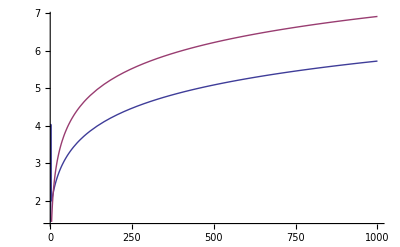

```mathematica
Plot[ {LogIntegral[LaguerreL[-2,Log[n]]]/LogIntegral[ n ],Log[n]},{n,1,1000}]
```

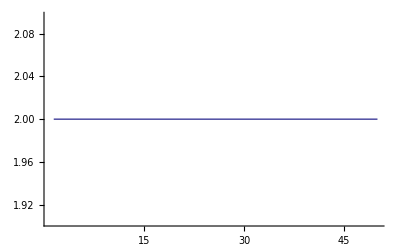

```mathematica
Plot[ {Log[n^2]/Log[ n ]},{n,1,50}]
```

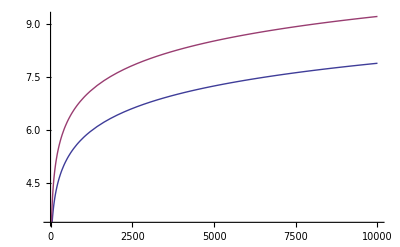

```mathematica
aa[n_] := LogIntegral[n]-Log[Log[n]]-EulerGamma
Plot[ {aa[LaguerreL[-2,Log[n]]]/aa[ n ],Log[n]},{n,0,10000}]
```

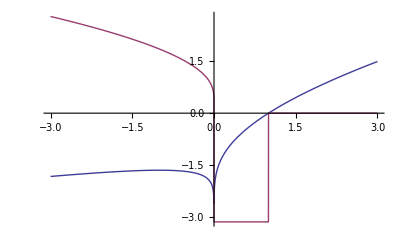

```mathematica
Plot[{ Re[aa[n]],Im[aa[n]]},{n,-3,3}]
```

```mathematica
Table[ {N[aa[n^3]/aa[ n ]]}/n^2,{n,1,100,1}]//TableForm
```

Infinity::indet: Indeterminate expression -EulerGamma + -∞ + ∞ encountered.

Indeterminate
1.18172
0.771132
0.603645
0.515533
0.462063
0.426513
0.401333
0.382652
0.368294
0.356948
0.34778
0.340235
0.333928
0.328588
0.324016
0.320064
0.316618
0.313591
0.310915
0.308535
0.306407
0.304496
0.302771
0.301209
0.299789
0.298494
0.29731
0.296224
0.295224
0.294303
0.293453
0.292665
0.291935
0.291256
0.290624
0.290035
0.289486
0.288972
0.288491
0.288041
0.287618
0.287221
0.286848
0.286497
0.286167
0.285855
0.285561
0.285284
0.285022
0.284774
0.28454
0.284319
0.284109
0.28391
0.283722
0.283544
0.283375
0.283214
0.283062
0.282917
0.28278
0.28265
0.282526
0.282409
0.282297
0.282191
0.28209
0.281994
0.281903
0.281817
0.281734
0.281656
0.281582
0.281512
0.281445
0.281381
0.281321
0.281264
0.28121
0.281158
0.281109
0.281063
0.281019
0.280978
0.280939
0.280902
0.280867
0.280834
0.280803
0.280774
0.280747
0.280721
0.280697
0.280675
0.280654
0.280634
0.280616
0.280599
0.280583

```mathematica
N@LaguerreL[-2,Log[10]]
```

33.0259

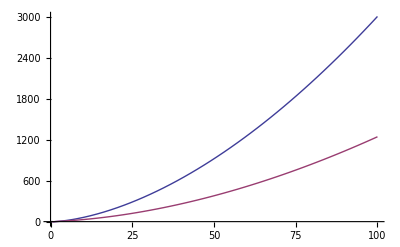

```mathematica
Plot[ {n LogIntegral[n], LogIntegral[n^2]},{n,0,100}]
```

```mathematica
Expand[D[LogIntegral[n^2]/LogIntegral[ n ],n]]
```

(2 n)/(Log[n^2] LogIntegral[n])-LogIntegral[n^2]/(Log[n] LogIntegral[n]^2)

```mathematica
Expand[Integrate[ D[ x^a,x]D[y^a,y],{x,1,n},{y,1,n/x}]]
```

ConditionalExpression[1-n^a+a n^a Log[n],Re[n]≥0||n∉Reals]

```mathematica
Expand[Integrate[ 1,{x,1,n^a},{y,1,n^a/x}]]
```

ConditionalExpression[1-n^a+n^a Log[n^a],Re[n^a]≥0||n^a∉Reals]

```mathematica
Chop@N[Gamma[2,0,-Log[n^a]]/Gamma[2]/.{n->20,a->3}]
```

63898.6

```mathematica
N[1-n^a+a n^a Log[n]/.{n->20,a->3}]
```

63898.6

```mathematica
N[1-n^a+n^a Log[n^a]/.{n->20,a->3}]
```

63898.6

```mathematica
Chop@N@Sum[ (-1)^(k+1)/k (-1)^k Gamma[k,0,-2Log[30]]/Gamma[k],{k,1,80}]
```

160.529

```mathematica
N@(LogIntegral[30^2]-Log[Log[30^2]]-EulerGamma)
```

160.529

```mathematica
N[Limit[ (LaguerreL[-(z),Log[30^2]]-1)/z,z->0]]
```

160.529

```mathematica
N[LogIntegral[30^2]-Log[Log[30^2]]-EulerGamma]
```

160.529

```mathematica
Expand@Integrate[ 1, {x,1,n^2},{y,1,n^2/x}]
```

ConditionalExpression[1-n^2+n^2 Log[n^2],Re[n^2]≥0||n^2∉Reals]

```mathematica
FullSimplify[( a x^a Log[ x] - x^a + 1) - (x Log[x] - x + 1)]
```

x-x^a+(-x+a x^a) Log[x]

```mathematica
Expand[(x^a-x)(a Log[x]-1)]
```

x-x^a-a x Log[x]+a x^a Log[x]

```mathematica
Expand@Integrate[ 1, {x,1,n^a},{y,1,n^a/x}]/Integrate[ 1, {x,1,n},{y,1,n/x}]
```

ConditionalExpression[(1-n^a+n^a Log[n^a])/(1+n (-1+Log[n])),(Re[n]≥0||n∉Reals)&&(Re[n^a]≥0||n^a∉Reals)]

```mathematica
-n^a-n (-1+Log[n])+n^a Log[n^a]
```

-n^a-n (-1+Log[n])+n^a Log[n^a]

```mathematica
FullSimplify[-n^a-n (-1+Log[n])+a n^a Log[n]]
```

n-n^a+(-n+a n^a) Log[n]

```mathematica
Expand[(1-n^a+n^a a Log[n])/(1+n (-1+Log[n]))]
```

```mathematica
FullSimplify[1/(1+n (-1+Log[n]))-n^a/(1+n (-1+Log[n]))+(a n^a Log[n])/(1+n (-1+Log[n]))]
```

(1+n^a (-1+a Log[n]))/(1-n+n Log[n])

```mathematica
Integrate[ 1, {x,1,(n)^a}]/Integrate[ 1, {x,1,(n)}]
```

(-1+n^a)/(-1+n)

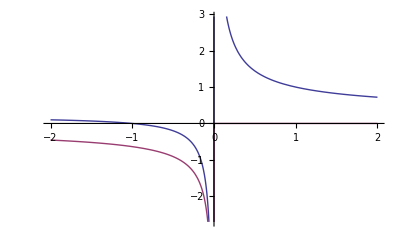

```mathematica
Plot[ {Re[(1/Log[n])(1-1/n)],Im[(1/Log[n])(1-1/n)]},{n,-2,2}]
```

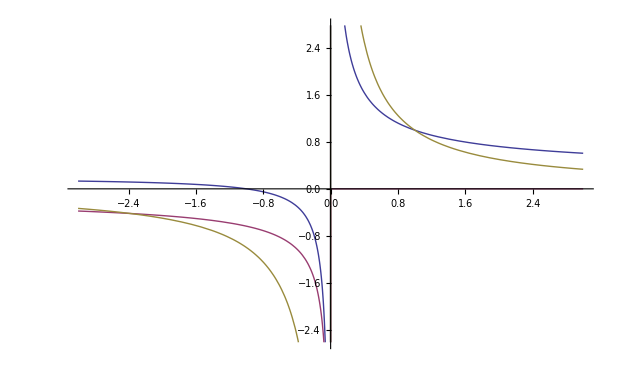

```mathematica
Plot[ {Re[(1/Log[n])(1-1/n)],Im[(1/Log[n])(1-1/n)],1/n},{n,-3,3}]
```

```mathematica
Integrate[(1/Log[n])(1-1/n),n]
```

-Log[Log[n]]+LogIntegral[n]

```mathematica
Limit[(1/Log[n])(1-1/n),n->-Infinity]
```

0

```mathematica
D[-Log[Log[n]]+LogIntegral[n]-EulerGamma,n]
```

1/Log[n]-1/(n Log[n])

```mathematica
Expand[Limit[(1/Log[n])(1-1/n)-EulerGamma,n->-1]]
```

-EulerGamma-(2 ⅈ)/π

```mathematica
N[-(2 ⅈ)/π]
```

0.-0.63662 ⅈ

```mathematica
Sum[ (-1)^k/(k!) Binomial[z,k]x^k,{k,0,Infinity}]
```

Hypergeometric1F1[-z,1,x]

```mathematica
Sum[ (-1)^k/(k!)Binomial[z,k]Log[n]^k,{k,0,Infinity}]
```

Hypergeometric1F1[-z,1,Log[n]]

```mathematica
Expand@LaguerreL[3,Log[12]]
```

1-3 Log[12]+(3 Log[12]^2)/2-Log[12]^3/6

```mathematica
Expand@Hypergeometric1F1[-3,1,Log[12]]
```

1-3 Log[12]+(3 Log[12]^2)/2-Log[12]^3/6

```mathematica
14*30000
```

420000